```mathematica
s = Import["/Users/thanedp/Documents/ion_clock_mahidol/DataAnalysis/Johnson_noise/2018_03_24/scope_57.csv"]
```

{{x-axis,1},{second,Volt},{-0.5,0.0044598},{-0.4995,0.0125},{-0.499,0.0173241},{-0.4985,0.0245603},{-0.498,0.0028518},{-0.4975,0.0229523},{-0.497,0.0173241},{-0.4965,0.0237563},{-0.496,0.0197362},{-0.4955,-0.0100126},{-0.495,0.0213442},{-0.4945,0.0068719},1974,{0.493,0.010892},{0.4935,-0.0035302},{0.494,0.0165201},{0.4945,0.0189322},{0.495,0.0125},{0.4955,0.0156658},{0.496,0.0044598},{0.4965,0.0164698},{0.497,0.001294},{0.4975,0.0148618},{0.498,0.0165201},{0.4985,-0.0003141},{0.499,0.010892},{0.4995,0.0012437}}
 |  |  |  |

```mathematica
s=Delete[s,1]
```

{{second,Volt},{-0.5,0.0044598},{-0.4995,0.0125},{-0.499,0.0173241},{-0.4985,0.0245603},{-0.498,0.0028518},{-0.4975,0.0229523},{-0.497,0.0173241},{-0.4965,0.0237563},{-0.496,0.0197362},{-0.4955,-0.0100126},{-0.495,0.0213442},{-0.4945,0.0068719},{-0.494,0.0060678},1973,{0.493,0.010892},{0.4935,-0.0035302},{0.494,0.0165201},{0.4945,0.0189322},{0.495,0.0125},{0.4955,0.0156658},{0.496,0.0044598},{0.4965,0.0164698},{0.497,0.001294},{0.4975,0.0148618},{0.498,0.0165201},{0.4985,-0.0003141},{0.499,0.010892},{0.4995,0.0012437}}
 |  |  |  |

```mathematica
s=Delete[s,1]
```

{{-0.5,0.0044598},{-0.4995,0.0125},{-0.499,0.0173241},{-0.4985,0.0245603},{-0.498,0.0028518},{-0.4975,0.0229523},{-0.497,0.0173241},{-0.4965,0.0237563},{-0.496,0.0197362},{-0.4955,-0.0100126},{-0.495,0.0213442},{-0.4945,0.0068719},{-0.494,0.0060678},{-0.4935,0.013304},1972,{0.493,0.010892},{0.4935,-0.0035302},{0.494,0.0165201},{0.4945,0.0189322},{0.495,0.0125},{0.4955,0.0156658},{0.496,0.0044598},{0.4965,0.0164698},{0.497,0.001294},{0.4975,0.0148618},{0.498,0.0165201},{0.4985,-0.0003141},{0.499,0.010892},{0.4995,0.0012437}}
 |  |  |  |

```mathematica
s
```

{{-0.5,0.0044598},{-0.4995,0.0125},{-0.499,0.0173241},{-0.4985,0.0245603},{-0.498,0.0028518},{-0.4975,0.0229523},{-0.497,0.0173241},{-0.4965,0.0237563},{-0.496,0.0197362},{-0.4955,-0.0100126},{-0.495,0.0213442},{-0.4945,0.0068719},{-0.494,0.0060678},{-0.4935,0.013304},1972,{0.493,0.010892},{0.4935,-0.0035302},{0.494,0.0165201},{0.4945,0.0189322},{0.495,0.0125},{0.4955,0.0156658},{0.496,0.0044598},{0.4965,0.0164698},{0.497,0.001294},{0.4975,0.0148618},{0.498,0.0165201},{0.4985,-0.0003141},{0.499,0.010892},{0.4995,0.0012437}}
 |  |  |  |

```mathematica
data=s[[All,2]]
```

{0.0044598,0.0125,0.0173241,0.0245603,0.0028518,0.0229523,0.0173241,0.0237563,0.0197362,-0.0100126,0.0213442,0.0068719,0.0060678,0.013304,0.0028518,0.0237563,0.0197362,0.0165201,0.0044598,0.0173241,0.0293844,0.0149121,0.0149121,0.0060678,-0.0043844,-0.0019724,0.011696,0.0165201,-0.0051884,0.013304,0.0221482,-0.0003643,0.0157161,0.010892,0.010892,0.0052638,0.0092839,-0.0067965,-0.0019724,0.0092839,0.0197362,-0.0108166,-0.0059925,0.0092839,0.0084799,0.0285804,0.0213442,-0.0108166,0.0125,-0.0140327,0.014108,0.0085302,0.0140578,0.0053141,0.003706,0.021294,0.0229523,0.0245101,0.0012437,0.0093342,0.0125,-0.0099623,0.014108,0.011696,0.0180779,0.023706,0.0036558,0.0117462,0.0188819,0.0261683,0.0204899,-0.0091583,0.0149121,-0.0003141,0.0245101,0.0085302,-0.0059422,-0.0131784,0.0181281,0.0052638,0.0068719,0.0245101,0.0180779,0.0085302,0.0061181,0.0245101,0.0045101,0.0093342,0.0204899,0.0196859,0.0132538,0.011696,0.0085302,-0.0075503,0.0180779,0.0100879,0.002098,0.0101382,0.0044598,-0.0035804,-0.0003141,0.011696,0.0084799,0.0053141,-0.0003643,0.0117462,0.013304,0.001294,-0.0051382,0.0181281,0.0156658,0.0061181,-0.0003643,-0.0067462,0.0285302,0.0077261,-0.0043342,0.0196859,0.0068719,0.0149121,0.0196859,0.001294,0.0188819,0.0164698,0.0044598,0.0069221,0.0173241,0.0125,0.011696,0.0196859,0.0069221,0.0109422,0.0053141,0.0140578,0.0357663,0.0140578,0.0245101,0.0044598,0.022098,0.0188819,0.013304,-0.0027261,0.0125,-0.0019221,0.0196859,0.0253141,0.0085302,0.0180779,0.0117462,0.0101382,-0.0147864,0.0100879,0.0069221,0.003706,0.0204899,0.0164698,0.0261181,-0.0011181,0.013304,0.021294,0.0077261,0.0061181,0.0100879,0.0077261,0.0180779,0.0053141,0.0301382,0.0148618,0.0164698,0.003706,0.0325503,0.003706,0.0277261,0.0148618,-0.0043342,0.0261181,0.0229523,0.0293342,-0.0011181,0.0068719,0.0165201,0.0061181,0.0180779,0.00049,0.0125,0.0157161,0.0053141,0.0109422,0.010892,0.0125,-0.0059422,0.0045101,0.0044598,0.002098,-0.0011181,0.010892,0.010892,0.0196859,0.0069221,0.0053141,0.00049,0.011696,0.0180779,0.0085302,0.0140578,0.0052638,0.0101382,0.0093342,0.0172739,0.0045101,0.0132538,0.0172739,0.0156658,0.0004397,-0.0107663,0.001294,0.0188819,0.0269221,0.0092839,0.0061181,0.002902,0.0077261,-0.0115704,0.0020477,0.0101382,0.0180779,-0.0092085,0.0204899,0.0204899,0.0085302,0.023706,0.0245603,0.0036558,0.003706,0.0196859,-0.0011181,0.003706,0.013304,0.011696,0.0060678,-0.0075503,0.0132538,-0.0099623,0.0053141,0.023706,0.0125,-0.0043844,0.011696,-0.0019221,0.0261181,0.0052638,0.013304,0.0269221,0.0052638,0.0069221,0.0028518,0.0245101,0.0093342,-0.0011181,0.011696,0.013304,0.0253141,-0.0027261,-0.0035302,0.0045101,0.0109422,0.001294,0.0140578,-0.0019221,0.022902,0.0253141,-0.0019221,0.0069221,0.0140578,0.00049,0.0028518,0.014108,0.0188819,0.0253141,0.0092839,0.002902,0.0068719,0.022098,0.022098,-0.0155905,0.0085302,0.0229523,0.0140578,-0.0043342,-0.0027261,0.0109422,0.0028518,0.0156658,-0.0107663,0.023706,0.021294,-0.0019221,0.0076759,0.0156658,0.0325503,-0.0019221,-0.0011181,0.0229523,0.0261181,-0.0075503,0.0069221,0.0204899,-0.0075503,-0.0019724,0.0132538,-0.0091583,0.0156658,0.0068719,0.0156658,0.0156658,0.0069221,0.0069221,0.0197362,0.022902,0.0084799,0.0140578,0.0084799,0.0004397,0.0092839,0.013304,0.003706,0.0061181,0.0076759,0.0189322,0.001294,0.001294,0.014108,0.011696,0.0061181,0.0132538,0.0092839,0.0092839,0.0092839,-0.0027261,0.0012437,-0.0027261,0.011696,0.0045101,0.0117462,0.0156658,0.0044598,0.0061181,0.0093342,0.0045101,0.0117462,0.011696,0.0229523,0.0334045,0.001294,-0.0019221,0.0060678,0.001294,0.014108,0.0188819,-0.0051382,0.001294,0.021294,0.0076759,0.0172739,0.023706,0.0076759,0.002098,-0.0059422,-0.0083543,0.011696,0.0164698,0.003706,0.0100879,-0.0003141,0.0084799,0.0245101,0.0061181,0.0117462,0.00049,0.0132538,0.0156658,0.0253141,0.010892,-0.0019221,0.0100879,0.0204899,-0.0043342,-0.0075503,0.0269221,0.0068719,0.0172739,0.0044598,-0.0003141,0.0156658,-0.0011181,0.0204899,0.0349623,0.0172739,0.00049,0.0085302,0.0301382,0.0061181,0.0132538,-0.0043844,0.0012437,-0.0027261,0.0196859,0.023706,0.0084799,0.0204899,0.0012437,0.0077261,0.0085302,-0.0107663,-0.0011181,0.0221482,0.0285302,-0.0123744,0.0261181,0.0132538,-0.0091583,0.00049,0.0069221,0.0012437,-0.0011181,0.0093342,0.0053141,0.0149121,-0.0051884,-0.0091583,0.0100879,0.0277764,0.0125,0.0204899,0.0148618,0.0196859,-0.0019221,0.003706,0.0060678,0.0125,0.0181281,0.0180779,0.001294,0.0148618,0.013304,0.010892,0.011696,0.0092839,0.0028518,0.022098,0.0076759,0.0245101,0.0132538,0.0053141,0.0069221,0.0028518,0.013304,0.0196859,-0.0027261,0.0125,0.0068719,0.0165201,0.001294,-0.0123744,0.0125,0.0028518,0.003706,0.0172739,0.0253141,0.0148618,-0.0019221,0.0060678,-0.0067462,-0.0003141,0.0245101,0.0077261,0.011696,-0.0043844,0.0245101,0.022098,0.0093342,0.0197362,0.0061181,-0.0035804,0.0028518,0.0053141,0.0053141,0.011696,0.0164698,-0.0043342,-0.0067462,0.021294,0.0180779,0.0164698,0.0053141,0.0045101,0.0245101,0.0132538,0.0100879,0.0148618,0.002902,0.0277261,0.0076759,0.023706,0.0165201,-0.0067462,0.0028518,0.014108,0.0196859,0.0045101,0.0180779,0.0204899,-0.0011181,0.0132538,0.0213442,0.0253141,-0.0043342,-0.0059422,0.0188819,0.0100879,0.0132538,-0.0067462,0.001294,0.0341583,-0.0180025,0.0164698,0.0148618,0.0269724,0.0044598,0.0140578,-0.0059422,0.0060678,0.0125,-0.0035302,0.0100879,0.0181281,0.0132538,-0.0043342,0.0140578,0.0077261,0.0285302,0.0196859,0.0196859,-0.0003141,0.0180779,-0.0027261,0.0132538,0.0253141,0.0028518,0.0068719,0.0020477,0.0068719,0.014108,0.0140578,0.003706,0.001294,-0.0035804,0.002902,0.0092839,0.0012437,0.0333543,0.003706,0.002902,0.002902,0.0172739,0.0084799,0.0164698,0.0245101,0.011696,0.0173241,0.0092839,0.0044598,0.010892,0.0213442,0.0028518,0.0309422,-0.0035804,0.0061181,0.0196859,0.001294,0.0044598,0.0053141,0.0084799,0.011696,0.003706,0.021294,0.0196859,0.023706,0.0053141,0.010892,0.0076759,0.0053141,0.00049,0.0237563,0.0077261,0.0101382,-0.0075503,0.014108,0.010892,0.011696,0.0181281,0.0020477,0.0100879,0.0180779,-0.0019724,-0.0019221,-0.0019221,0.0109422,0.0085302,0.0197362,0.0149121,0.0173241,0.0140578,0.0109422,0.0173241,0.0148618,0.0140578,0.0084799,0.023706,0.0093342,0.010892,0.00049,0.010892,0.0085302,0.0156658,0.0285302,0.022902,-0.0051884,0.013304,0.0365704,0.0196859,0.0028518,0.0189322,0.0077261,0.0053141,0.002902,0.0165201,0.0196859,0.0269221,0.0173241,-0.0019221,0.0053141,0.0156658,0.021294,0.0181281,0.0053141,0.0101382,0.0181281,0.0173241,0.0045101,0.002902,0.00049,0.0045101,0.0149121,-0.0011181,0.0036558,-0.0147864,0.0204899,0.0125,0.0132538,0.0269221,0.0245603,0.0085302,0.0085302,0.0148618,0.0076759,0.0221482,0.0125,0.0076759,0.0325503,0.0053141,0.0068719,-0.0003141,0.0069221,-0.0067462,0.001294,0.0149121,0.021294,0.022098,0.0205402,-0.0003141,0.0044598,0.022098,0.002902,0.0020477,0.003706,0.0148618,0.0188819,0.002902,0.0100879,0.0389824,0.00049,0.0148618,0.0052638,0.0157161,0.002902,-0.0019724,-0.0019221,-0.0123744,0.0188819,-0.0027261,0.0060678,0.0069221,0.002902,0.0204899,0.0125,0.0125,0.002902,0.001294,0.0101382,0.0164698,0.002098,0.0125,0.0148618,0.0253141,0.014108,0.014108,-0.0003643,-0.0019221,0.003706,0.0085302,0.0060678,-0.0043342,0.022098,0.0036558,-0.0003141,0.0277764,0.0149121,-0.0003643,0.0148618,0.0180779,0.002902,0.0100879,0.0068719,-0.0019221,0.0125,0.001294,0.0125,0.0077261,0.0237563,-0.0019724,0.0101382,0.023706,0.0188819,0.0093342,-0.0035302,0.0036558,0.0077261,0.0109422,0.013304,0.0156658,0.0117462,0.0277261,0.0164698,0.0181281,0.0109422,-0.0051382,0.0061181,0.0397864,0.002098,0.0349623,-0.0075503,-0.0003141,0.0269221,0.0125,0.010892,0.0132538,-0.0067462,0.0053141,0.0069221,0.011696,0.013304,0.0204899,0.0172739,0.0084799,0.0076759,0.0132538,0.0148618,0.001294,0.0093342,-0.0027261,0.002098,0.0165201,-0.0067462,0.0149121,0.0204899,0.0245101,0.00049,0.0164698,0.0100879,0.0309422,0.0069221,0.0180779,-0.0027261,0.002098,-0.0067462,0.0165201,0.014108,0.0261181,0.0149121,0.002902,-0.0115704,0.0132538,0.0117462,0.022902,0.0117462,0.0045101,0.003706,0.0101382,0.0197362,0.0261181,0.0125,-0.0003141,0.0100879,0.011696,0.023706,0.0061181,0.0317462,0.0188819,0.0077261,0.0213442,-0.0067462,0.0045101,0.001294,0.0245101,0.0045101,-0.0019221,0.0069221,0.0117462,0.0172739,0.0165201,0.0164698,0.002902,0.0060678,0.0245101,0.0245101,0.011696,0.0204899,0.0053141,0.0149121,0.0093342,-0.0043844,0.0180779,-0.0043342,0.0052638,0.011696,0.0173241,0.0245603,0.0173241,-0.0019221,0.0012437,0.00049,0.0245101,0.0205402,-0.0027261,0.0036558,0.0012437,-0.0003141,0.0077261,0.0077261,0.0156658,0.011696,0.0253141,0.0173241,0.0053141,-0.0059422,0.013304,0.0148618,-0.0147864,0.0092839,0.0132538,0.001294,0.0012437,0.013304,0.0181281,0.0172739,-0.0027261,0.0125,0.0004397,0.0069221,0.00049,0.0149121,0.002902,0.0277261,-0.0019221,-0.0035302,0.002098,0.011696,0.0165201,0.0004397,0.0036558,-0.0091583,0.0117462,0.0093342,0.0052638,0.022098,0.0077261,0.0109422,0.0204899,0.011696,0.0085302,0.0132538,0.0140578,0.002902,0.0068719,-0.0107663,0.0125,0.0045101,0.0213442,0.0164698,0.0076759,0.0293342,0.0100879,0.011696,0.0229523,-0.0003141,0.0077261,-0.0075503,-0.0019724,0.0149121,-0.0011181,0.0092839,0.00049,0.0261181,0.0125,-0.0035302,0.0132538,0.023706,0.0045101,-0.0011181,-0.0011181,0.0061181,0.0109422,0.010892,0.0125,0.0084799,0.0053141,0.002902,0.0148618,0.0157161,0.0189322,0.0172739,0.0004397,0.0261181,0.0381784,0.0069221,0.0204899,0.0117462,-0.0011181,0.0140578,0.0180779,0.0069221,0.0245101,0.0245101,0.0204899,0.0044598,0.0117462,0.0093342,0.0085302,0.0132538,0.0196859,0.0069221,0.0125,0.0093342,0.010892,0.002902,0.0084799,0.0084799,0.0068719,0.0093342,0.0036558,0.0125,0.002098,0.023706,0.0132538,-0.0051382,0.0093342,0.0076759,0.0053141,0.0069221,0.0100879,-0.0043844,-0.0051382,0.0053141,0.0092839,0.0101382,0.0172739,0.0093342,0.003706,0.0125,0.0004397,0.0052638,0.0045101,0.0093342,0.0077261,0.0253643,0.0125,0.0181281,0.0213442,0.0053141,0.0301382,0.0084799,0.0140578,-0.0043844,0.003706,0.002902,0.0277764,0.0117462,0.0084799,0.00049,0.0148618,0.0180779,0.0188819,0.0084799,0.0077261,0.022902,0.021294,0.0245101,0.0172739,0.0261683,0.0157161,0.0221482,0.0157161,0.0261181,0.0253141,0.014108,0.0196859,0.0164698,0.0197362,0.0157161,0.0084799,-0.0091583,-0.0035302,-0.0003141,0.0077261,0.0156658,0.0125,0.010892,0.0109422,0.0028518,-0.0011181,0.0196859,-0.0027261,0.0076759,0.0068719,-0.0019724,0.0085302,0.0309422,0.0132538,0.0117462,-0.0107663,0.0213442,0.0020477,0.0389824,-0.0027261,-0.0067462,0.010892,0.0052638,0.0277764,0.0068719,0.0221482,0.0188819,0.0044598,0.0036558,-0.0019221,0.0140578,0.0125,0.0132538,0.0253141,0.0172739,0.010892,-0.0019221,0.0253141,-0.0067462,0.0172739,-0.0027261,0.0333543,0.0156658,-0.0011181,0.0229523,0.0085302,-0.0084045,0.0188819,0.0092839,0.013304,0.0020477,0.0100879,0.0109422,0.0293342,0.0157161,0.0125,0.0237563,0.0092839,0.0229523,-0.0139824,-0.0043844,0.0077261,0.0093342,0.0125,0.0245101,0.021294,0.0092839,0.0101382,-0.0091583,0.0028518,0.0084799,0.0109422,0.022098,0.0125,0.011696,0.0100879,0.0277764,0.011696,0.013304,0.0132538,0.0148618,-0.0003141,-0.0011181,0.022098,0.0069221,0.0148618,0.0101382,-0.0228266,0.0157161,0.0164698,0.0061181,0.0285302,0.011696,-0.0019724,0.0101382,0.010892,0.0140578,0.0149121,0.002902,0.0125,0.0204899,-0.0011181,-0.0035302,0.0132538,0.0052638,-0.0100126,0.011696,0.0092839,-0.0067462,0.0084799,0.0157161,0.0148618,0.011696,-0.0099623,0.003706,0.0149121,0.0101382,0.0140578,0.0060678,0.0205402,0.0180779,0.011696,0.0012437,-0.0099623,0.0140578,0.0140578,0.0077261,0.0028518,0.0044598,-0.0019221,-0.0019724,0.022098,0.0092839,0.0068719,0.0077261,0.0004397,0.0165201,-0.0019221,-0.0131784,0.0165201,0.0173241,0.0045101,0.001294,0.002098,-0.0003141,0.010892,0.0149121,0.010892,0.0045101,0.0189322,0.0085302,0.0053141,0.013304,0.0261181,0.0293342,0.0061181,0.014108,0.001294,0.0132538,0.0036558,0.0164698,0.002098,0.0084799,-0.0027261,0.0053141,-0.0147864,0.023706,0.0028518,0.0172739,-0.0019221,0.0285302,0.0101382,0.001294,-0.0043342,0.0068719,0.010892,-0.0043342,0.0045101,0.011696,-0.0107663,-0.0003643,-0.0076005,0.014108,0.0036558,-0.0067462,-0.0067462,0.0020477,0.0101382,0.0100879,-0.0027764,0.0085302,0.0165201,0.0069221,0.0085302,0.021294,0.0076759,0.021294,0.002902,0.0165201,-0.0051382,0.014108,0.001294,0.011696,0.0132538,-0.0027261,0.0221482,0.0140578,0.0172739,0.0092839,0.0092839,-0.0099623,0.001294,-0.0035302,0.022098,0.0165201,0.003706,-0.0051382,0.0317462,0.0237563,0.0149121,-0.0123744,0.0045101,0.0188819,0.0341583,0.0164698,0.0084799,0.0180779,0.0060678,0.0004397,0.0069221,0.0293342,0.0196859,-0.0123744,0.0165201,0.0140578,0.0045101,0.0068719,-0.0043342,0.0157161,0.0196859,0.0052638,-0.0059422,0.0052638,0.0148618,0.0053141,0.0333543,-0.0043342,0.0060678,0.0060678,0.0132538,0.001294,0.0156658,0.011696,-0.0131784,0.0044598,0.0164698,0.0100879,-0.0019221,0.0149121,-0.0011181,0.0253141,0.0253141,-0.0083543,0.0100879,0.0245101,0.0101382,0.0093342,-0.0083543,-0.0043844,0.0125,0.0125,-0.0067462,0.0109422,0.00049,0.0101382,0.0245101,0.011696,-0.0075503,0.0140578,-0.0027261,0.011696,0.0125,0.022902,0.0077261,-0.0011181,-0.0027764,0.0036558,0.0045101,0.0180779,0.0156658,0.0085302,-0.0115704,0.0204899,0.0084799,0.0277261,0.0020477,0.003706,0.0077261,0.0004397,0.0085302,0.0069221,0.0101382,0.0068719,0.0173241,-0.0083543,0.0188819,-0.0075503,0.0093342,-0.0067462,0.0045101,0.0093342,-0.0027764,0.0100879,0.011696,0.0101382,0.0052638,-0.0003141,0.0068719,0.0100879,0.003706,-0.0123744,0.0197362,0.0165201,0.0165201,0.0045101,0.002098,0.022098,0.0100879,-0.0075503,0.0085302,-0.0076005,0.0061181,0.0140578,0.0085302,0.0261181,0.0125,0.0172739,-0.0011181,0.0100879,0.0077261,0.013304,0.0148618,0.0100879,0.0196859,0.0053141,0.0140578,0.0084799,0.0245603,0.0261181,0.0172739,0.0149121,0.0204899,0.0076759,0.0076759,0.0196859,-0.0027261,0.0148618,-0.0171985,0.001294,0.022098,0.011696,0.014108,0.014108,0.0061181,-0.0011683,0.0076759,0.0085302,0.013304,0.0132538,0.0052638,0.002902,-0.0011683,0.022902,0.0204899,0.0157161,0.0101382,0.0044598,0.0100879,0.0180779,0.0196859,0.0101382,-0.0003141,0.0084799,0.0293342,0.0125,0.014108,0.0077261,-0.0051382,0.011696,0.0085302,0.001294,-0.0051382,0.0045101,0.0020477,0.0205402,0.0180779,-0.0059925,0.0164698,-0.0035302,0.0069221,-0.0011683,-0.0099623,0.0060678,0.0109422,0.0060678,0.00049,0.0085302,0.010892,-0.0019724,0.0069221,0.0060678,0.0253141,0.011696,0.0221482,0.0164698,0.0180779,-0.0027261,0.0301382,0.0093342,0.0140578,-0.0019221,0.0125,0.0060678,0.003706,-0.0019221,0.0156658,0.0180779,0.0085302,0.0253141,0.0196859,0.021294,0.0044598,0.0125,0.0148618,-0.0075503,0.0285302,0.0028518,0.0132538,0.0148618,-0.0019221,-0.0139824,0.0172739,0.022098,0.0077261,0.0204899,-0.0043342,0.0180779,0.0093342,0.0092839,0.002098,0.0245101,0.0093342,0.00049,0.0100879,0.0261181,0.0045101,-0.0075503,-0.0115704,0.0204899,0.0117462,0.0093342,0.013304,-0.0003141,0.0173241,0.0060678,0.0180779,0.0077261,0.013304,0.0148618,0.0285302,0.0036558,0.0132538,0.0285302,0.002098,0.0092839,0.0044598,0.0277261,0.0196859,0.023706,0.0085302,0.0069221,0.0173241,0.0061181,0.0140578,0.021294,0.0028518,0.023706,-0.0027261,0.0132538,0.0045101,0.0100879,0.0172739,0.0269221,0.014108,0.0053141,-0.0043342,0.0053141,0.0117462,0.0173241,0.0084799,0.0261181,0.0156658,0.0068719,0.0036558,0.0044598,0.0060678,0.010892,0.014108,0.0109422,0.0301382,0.0109422,0.0093342,0.0077261,0.013304,0.0117462,0.002902,-0.0059422,0.021294,0.002098,0.013304,-0.0003141,0.0157161,0.0045101,0.0076759,0.0197362,0.0197362,0.0077261,-0.0075503,-0.0035302,-0.0075503,0.0069221,0.0061181,0.002902,0.0156658,0.0036558,0.0109422,0.002902,0.0061181,-0.0076005,0.0045101,0.0077261,0.0180779,0.0053141,0.0333543,0.0180779,0.0076759,0.0140578,0.014108,0.011696,0.0172739,0.0172739,0.0092839,0.0069221,0.0156658,0.0132538,0.0125,0.0084799,-0.0067462,0.001294,0.0125,0.0125,0.0077261,0.0068719,-0.0019221,0.0101382,0.0204899,-0.0027261,0.0172739,0.0269221,0.003706,0.002902,0.0173241,0.0125,-0.0075503,0.0125,0.0036558,0.0125,0.0077261,-0.0107663,0.0148618,0.0101382,0.0109422,0.0117462,-0.0043844,0.0045101,0.0172739,0.0172739,0.0093342,0.021294,0.0068719,0.0093342,0.0148618,0.0245101,0.0188819,0.0076759,0.0196859,0.0261181,0.0156658,-0.0091583,0.0221482,-0.0083543,0.0269221,0.0109422,0.003706,0.022098,0.0077261,0.0245101,0.010892,0.0164698,0.0125,0.010892,0.0245603,0.0060678,0.0172739,0.0125,0.022098,0.0253141,0.0004397,0.0157161,0.0092839,0.002098,-0.0059422,0.021294,0.0148618,0.0173241,-0.0083543,0.0004397,0.0085302,0.0285302,0.0140578,0.0068719,0.0196859,0.0164698,0.0020477,0.0069221,0.022902,-0.0051382,0.0196859,0.0045101,0.0101382,0.0077261,0.0045101,0.0149121,0.0068719,-0.0091583,-0.0019221,0.0132538,0.0140578,0.0068719,0.0165201,-0.0083543,0.0084799,0.0076759,-0.0027261,-0.0076005,0.0004397,0.0132538,0.0197362,0.0148618,0.002902,0.002098,0.013304,0.0140578,0.021294,0.0084799,0.022902,0.0117462,0.0068719,0.022098,0.0245101,0.011696,0.00049,0.021294,0.0165201,0.0269724,0.0125,0.00049,-0.0019221,0.0140578,0.0180779,0.0140578,0.021294,0.0196859,0.0077261,0.0060678,-0.0075503,0.0045101,0.0093342,0.0044598,-0.0091583,0.0164698,-0.0107663,0.0045101,0.0028518,0.013304,0.0421985,0.0156658,0.00049,0.0156658,-0.0003141,0.011696,0.0053141,0.0028518,-0.0019221,-0.0019724,0.0052638,0.0301884,0.0077261,0.0253141,0.013304,0.0188819,0.0261181,0.0125,0.0076759,0.0204899,0.0036558,-0.0083543,0.0245603,0.0221482,0.0100879,0.0204899,0.0085302,0.022902,0.0069221,-0.0075503,0.003706,0.0053141,0.002902,0.014108,0.0053141,0.00049,0.0069221,0.0085302,0.0109422,0.002902,0.0092839,0.0060678,-0.0083543,0.0309422,-0.0075503,0.0125,0.0157161,0.0180779,0.0109422,0.0101382,0.0117462,0.0100879,0.0068719,-0.0027261,0.0093342,0.011696,0.0069221,-0.0155905,0.013304,0.0125,0.0164698,0.0188819,0.0061181,0.003706,0.0172739,-0.0115704,0.0245101,0.0100879,0.0077261,0.0173241,0.0221482,0.00049,0.002902,-0.0051884,0.0309422,0.0181281,0.0132538,-0.0035302,0.0269724,0.0157161,0.0045101,0.013304,0.0277261,0.0052638,0.010892,0.0189322,0.0148618,0.0157161,-0.0019724,-0.0083543,0.0125,0.0245101,0.0253141,0.0156658,0.013304,0.0053141,0.00049,0.002098,0.00049,0.010892,0.0020477,-0.0019221,0.003706,0.0044598,0.0173241,0.0093342,0.0285302,0.0180779,0.0085302,0.021294,0.0053141,0.0285302,0.0068719,0.0076759,0.022098,-0.0003141,0.0125,0.0157161,-0.0123744,-0.0059925,0.0045101,0.0101382,0.0125,-0.0003141,-0.0051382,0.002098,0.0012437,0.0045101,0.003706,0.0149121,0.0109422,0.022098,0.0365704,0.0229523,-0.0051382,0.0053141,0.0084799,0.0261683,0.0148618,0.0092839,0.0237563,-0.0075503,0.0061181,0.001294,0.0173241,0.0076759,0.0012437,0.0060678,0.0277764,0.0125,0.0180779,0.0060678,0.0069221,0.0301382,-0.0043342,0.0277261,-0.0019221,0.011696,-0.0027261,0.0044598,0.0181281,0.010892,0.022098,0.0012437,0.0092839,0.00049,0.022098,0.003706,0.0269221,0.0189322,0.0245101,0.0285804,0.0172739,0.014108,0.0156658,0.003706,0.0172739,-0.0075503,0.0061181,0.0309422,0.0085302,0.0068719,-0.0196106,0.010892,0.0189322,0.010892,0.0269221,0.0196859,0.0045101,0.0196859,0.0076759,0.0085302,0.0109422,0.0253141,0.0149121,-0.0051382,0.0093342,0.0093342,0.0164698,0.0189322,0.001294,0.0101382,0.0092839,0.0061181,0.0156658,0.0101382,0.023706,0.0157161,0.0028518,0.0140578,0.002098,0.003706,0.0140578,0.0068719,0.0204899,-0.0131784,0.0109422,0.0028518,0.0045101,0.0060678,0.011696,-0.0011181,0.0253141,-0.0059422,-0.0027261,0.002902,0.013304,0.0180779,0.0421985,-0.0019221,0.0053141,0.0085302,0.003706,0.0028518,0.0093342,-0.0051382,-0.0011181,0.011696,-0.0107663,0.0061181,-0.0131784,0.002098,0.011696,0.0132538,0.0430025,0.0125,0.0189322,0.0061181,0.0125,0.003706,0.0165201,0.0197362,-0.0035302,0.0060678,0.0197362,0.0068719,0.010892,-0.0035302,0.0165201,0.0189322,0.0125,0.0156658,0.0044598,0.0164698,0.001294,0.0148618,0.0165201,-0.0003141,0.010892,0.0012437}

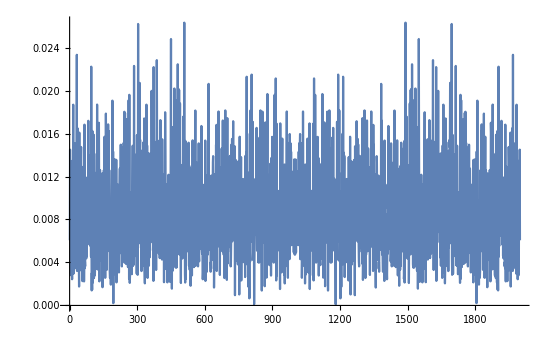

```mathematica
ListLinePlot[Delete[Abs[Fourier[data]],1],PlotRange->All]
```